# Helpful Mathematica code v2

## Plotting

### Functions

plotinator
Plots functions with labeled key points. For the values of key points and asymptotes, hover you mouse over them.
The syntax is basically the same as Plot however it does not accept extra arguments like plot range

```mathematica
plotinator[function,{variable,min,max}]
plotinator[{function1,function2,...},{variable,min,max}]
```

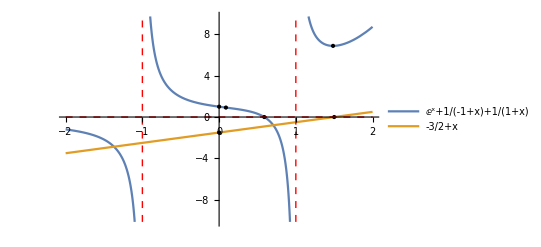

```mathematica
plotinator[{ⅇ^x+1/(x-1)+1/(x+1),x-3/2},{x,-2,2}]
```

### Probability

#### Normal Distribution

plotNormalDistributionBetween
Plots probability density functions and shades the desired area. The by default the function will show 4 standard deviations either side of the mean. Supplying standardDeviationsToShow parameter can change this

```mathematica
plotNormalDistributionBetween[mean,standardDeviation,min,max]
plotNormalDistributionBetween[mean,standardDeviation,min,max,standardDeviationsToShow]
```

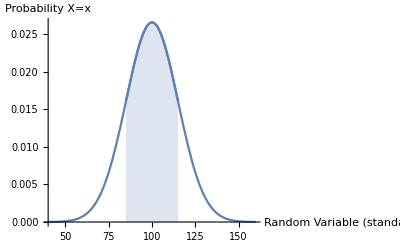

```mathematica
plotNormalDistributionBetween[100,15,85,115]
```

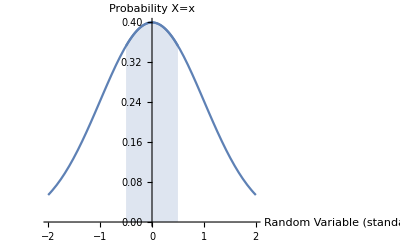

```mathematica
plotNormalDistributionBetween[0,1,-0.5,0.5,2]
```

plotNormalDistributionGreaterThan
Plots probability density functions and shades the desired area. The by default the function will show 4 standard deviations either side of the mean. Supplying standardDeviationsToShow parameter can change this. The standardDeviationsToShow parameter is the same as in plotNormalDistributionBetween.

```mathematica
probabilityNormalDistributionGreaterThan[mean,standardDeviation,min]
probabilityNormalDistributionGreaterThan[mean,standardDeviation,min,standardDeviationsToShow]
```

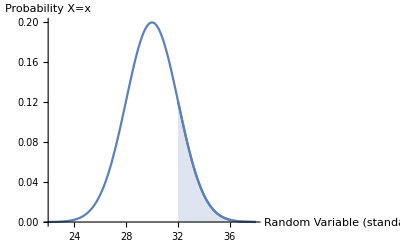

```mathematica
plotNormalDistributionGreaterThan[30,2,32]
```

plotNormalDistributionLessThan
Plots probability density functions and shades the desired area. The by default the function will show 4 standard deviations either side of the mean. Supplying standardDeviationsToShow parameter can change this. The standardDeviationsToShow parameter is the same as in plotNormalDistributionBetween.

```mathematica
plotNormalDistributionLessThan[mean,standardDeviation,max]
plotNormalDistributionLessThan[mean,standardDeviation,max,standardDeviationsToShow]
```

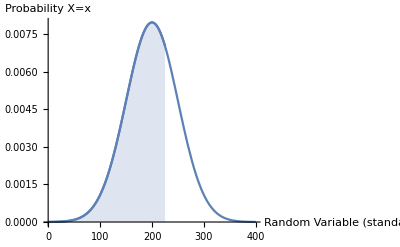

```mathematica
plotNormalDistributionLessThan[200,50,225]
```

#### Binomial Distribution

plotBinomialDistributionBetweenInclusive
Plots the discrete binomial distribution with n trails and p chance of success, highlighting between a and b, including a and b.

```mathematica
plotBinomialDistributionBetweenInclusive[n,p,a,b]
```

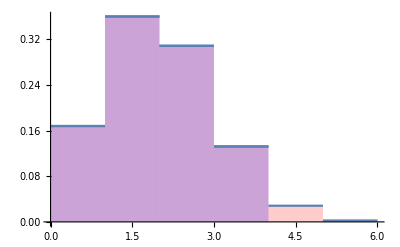

```mathematica
plotBinomialDistributionBetweenInclusive[5,0.3,0,3]
```

plotBinomialDistributionBetweenExclusive
Plots the discrete binomial distribution with n trails and p chance of success, highlighting between a and b, NOT including a and b.

```mathematica
plotBinomialDistributionBetweenExclusive[n,p,a,b]
```

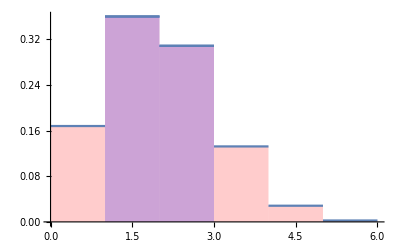

```mathematica
plotBinomialDistributionBetweenExclusive[5,0.3,0,3]
```

plotBinomialDistributionEquals
Plots the discrete binomial distribution with n trails and p chance of success, highlighting all values equal to a

```mathematica
plotBinomialDistributionEquals[n,p,a]
```

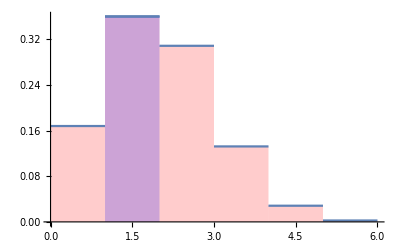

```mathematica
plotBinomialDistributionEquals[5,0.3,1]
```

plotBinomialDistributionGreaterThan
Plots the discrete binomial distribution with n trails and p chance of success, highlighting all values greater than a

```mathematica
plotBinomialDistributionGreaterThan[n,p,a]
```

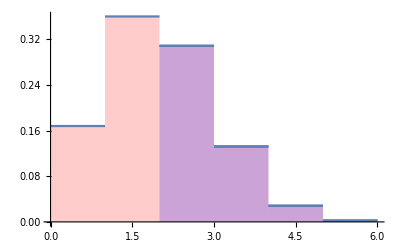

```mathematica
plotBinomialDistributionGreaterThan[5,0.3,1]
```

plotBinomialDistributionLessThan
Plots the discrete binomial distribution with n trails and p chance of success, highlighting all values less than a

```mathematica
plotBinomialDistributionLessThan[n,p,a]
```

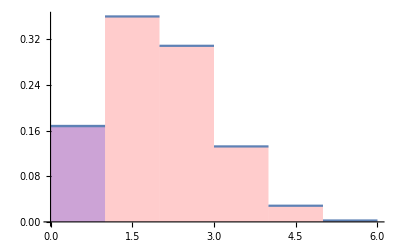

```mathematica
plotBinomialDistributionLessThan[5,0.3,1]
```

### Euler’s Method (specialist)

eulersMethodPlot
Plots the Euler’s method approximation along with the correct solution from DSolve. The gradient should NOT include y’[x]==. The domain implicitly specifies the final x value. The increment is how much the function increases by each iteration. x0 and y0 are the initial conditions for the differential equations and where the plot will start.

```mathematica
eulersMethodPlot[gradient,{x,min,max},y,{x0,y0},increment]
```

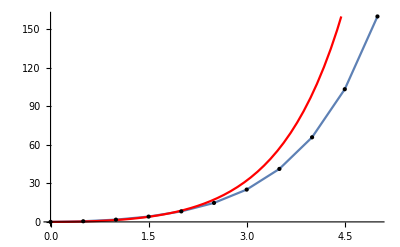

```mathematica
eulersMethodPlot[2x+y,{x,0,5},y,{0,0},0.5]
```

### Complex Numbers (specialist)

complexPlot
Plots regions of the complex plain. The variable represents the complex number for which the region is define as the set of solutions. Most commonly the variable is z.

```mathematica
complexPlot[equasion,variable,{xmin,xmax},{ymin,ymax}]
```

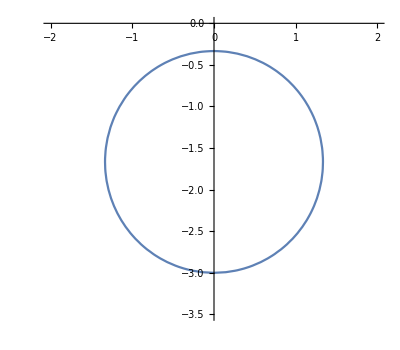

```mathematica
complexPlot[Norm[z-ⅈ]==2Norm[z+ⅈ],z,{-2,2},{-3.5,0}]
```

### Vectors (specialist)

geogebra3DSeption
Plots vectors like Geogebra. There is not way to plot planes or equations in this version. Clicking and dragging will rotate the view. Holding control while clicking and dragging will scale the view. Holding shift while clicking and dragging will scale the view.

```mathematica
geogebra3DSeption[vectors]
```

```mathematica
geogebra3DSeption[{{{0,0,0},{3,4,5}},vectorOrigin[2,1,3],vectorFrom[2,3,1,-1,2,3]}]
```

-Graphics3D-

```mathematica
Manipulate[geogebra3DSeption[{vectorOrigin[1,1,0],vectorOrigin[-1,a,0]}],{a,-1,1}]
```

### Approximate Integrals

approximateIntegralPlot
Plots the rectangular approximation of the integral of the function, function in variable between min and max where are the rectangles start at the direction end point and are spaced every increment. The direction MUST either be “left” or “right” keeping the quotation marks.

```mathematica
approximateIntegral[function,{variable,min,max},direction,increment]
```

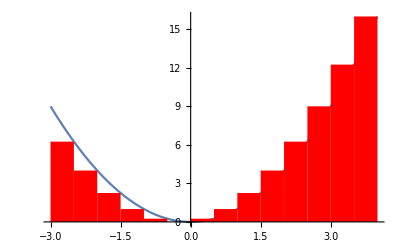

```mathematica
approximateIntegralPlot[x^2,{x,-3,4},"right",0.5]
```

## Calculus

### Key Points

roots
Calculates the roots of a function (f(x)=0) and returns then in the form of a list of x,y points

```mathematica
roots[function,variable]
```

```mathematica
roots[ⅇ^x+1/(x-1)+1/(x+1),x]
```

{{0.59,0}}

```mathematica
roots[ⅇ^x+1/(x-1)+1/(x+1),x,1≤x]
```

{}

```mathematica
roots[x^2-1,x]
```

{{-1,0},{1,0}}

turningPoints
Calculates all turning points (f’(x)=0) of a function and returns them in the form of list of x,y points

```mathematica
turningPoints[function,variable]
```

```mathematica
turningPoints[ⅇ^x+1/(x-1)+1/(x+1),x]
```

{{1.5,7.}}

maximumTurningPoints
Calculates all turning points (f’(x)=0,f’’(x)<0) of a function and returns them in the form of list of x,y points

```mathematica
maximumTurningPoints[function,variable]
```

```mathematica
maximumTurningPoints[ⅇ^x+1/(x-1)+1/(x+1),x]
```

{}

minimumTurningPoints
Calculates all turning points (f’(x)=0,f’’(x)>0) of a function and returns them in the form of list of x,y points

```mathematica
minimumTurningPoints[function,variable]
```

```mathematica
minimumTurningPoints[ⅇ^x+1/(x-1)+1/(x+1),x]
```

{{1.5,7.}}

stationaryPointsOfInflection
Calculates all stationary points of inflection (f’’(x)=0,f’(x)=0,f’’’(x)=0) of a function and returns them in the form of list of x,y points

```mathematica
stationaryPointsOfInflection[function,variable]
```

```mathematica
stationaryPointsOfInflection[ⅇ^x+1/(x-1)+1/(x+1),x]
```

{}

movingPointsOfInflection (specialist)
Calculates all moving points of inflection (f’’(x)=0,f’(x)≠0,f’’’(x)=0) of a function and returns them in the form of list of x,y points

```mathematica
movingPointsOfInflection[function,variable]
```

```mathematica
movingPointsOfInflection[ⅇ^x+1/(x-1)+1/(x+1),x]
```

{{0.089,0.91}}

### Asymptotes

horizontalAsymptotes
calculates the horizontal asymptotes in the form y=a where the output is the list of values of a

```mathematica
horizontalAsymptotes[function,variable]
```

```mathematica
horizontalAsymptotes[ⅇ^x+1/(x-1)+1/(x+1),x]
```

{0}

verticleAsymptotes
calculates the vertical asymptotes in the form x=a where the output is the list of values of a

```mathematica
verticleAsymptotes[function,variable]
```

```mathematica
verticleAsymptotes[ⅇ^x+1/(x-1)+1/(x+1),x]
```

{-1,1}

obliqueAsymptotes (specialist)
calculates the oblique asymptotes in the form y=f(x) where the output is the list of values of f(x)

```mathematica
obliqueAsymptote[function,variable]
```

```mathematica
obliqueAsymptote[ⅇ^x+1/(x-1)+1/(x+1),x]
```

{ⅇ^x}

### Approximate Integrals

approximateIntegral
Calculates the rectangular approximation of the integral of the function, function in variable between min and max where are the rectangles start at the direction end point and are spaced every increment. The direction MUST either be “left” or “right” keeping the quotation marks.
Bellow is an illustration of what the function is doing.

```mathematica
approximateIntegral[function,{variable,min,max},direction,increment]
```

```mathematica
approximateIntegral[x^2,{x,0,4},"left",1]
```

14

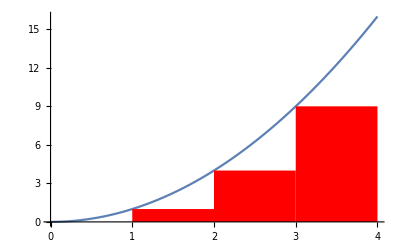

### Techniques of differentiation (specialist)

implicityD
Calculates the implicit derivative of the equation where variable1 is a function of variable2 (variable2(variable1))

```mathematica
implicityD[equasion,variable1,variable2]
```

```mathematica
implicityD[y^2==x^2,x,y]
```

2 y[x] y'[x]==2 x

solveForDyDx
Rearranges an equation in terms of dy/dx where variable1 is dy and variable2 is dx and variable1 is a function of variable2 (variable2(variable1))

```mathematica
solveForDyDx[equasion,variable1,variable2]
```

```mathematica
solveForDyDx[2 y[x] y'[x]==2 x,x,y]
```

{{y'[x]→x/y[x]}}

D2
Calculates the second derivative of a function

```mathematica
D2[function,variable]
```

```mathematica
D2[x^2,x]
```

2

### Solids of Revolution (specialist)

solidOfRevolutionAroundY
Calculates the solid of revolution around the y axis where y, x is the function y(x) between a and b. do NOT enter the function y^2(x)

```mathematica
solidOfRevolutionAroundY[y,x,a,b]
```

```mathematica
solidOfRevolutionAroundY[x,x,0,2]
```

(8 π)/3

solidOfRevolutionAroundX
Calculates the solid of revolution around the x axis where x, y is the function x(y) between a and b. do NOT enter the function x^2(y)

```mathematica
solidOfRevolutionAroundY[x,y,a,b]
```

```mathematica
solidOfRevolutionAroundX[√y,y,0,2]
```

2 π

nSolidOfRevolutionAroundY
Calculates the numeric approximation of the solid of revolution around the y axis where y, x is the function y(x) between a and b. do NOT enter the function y^2(x)

```mathematica
nSolidOfRevolutionAroundY[x,y,a,b]
```

nSolidOfRevolutionAroundY
Calculates the numeric approximation of the solid of revolution around the y axis where y, x is the function y(x) between a and b. do NOT enter the function y^2(x)

```mathematica
nSolidOfRevolutionAroundX[y,x,a,b]
```

### Bounded and Enclosed Area

Calculates the bounded area of a function between min and max and shows the different sub integrals that must be computed.

```mathematica
boundedArea[function,{variable,min,max}]
```

```mathematica
boundedArea[x^3-7x+6,{x,-3,2}]
```

Abs[∫_-3^1 (6-7 x+x^3)ⅆx]==32

Abs[∫_1^2 (6-7 x+x^3)ⅆx]==3/4

131/4

enclosedArea
Calculates the area enclosed by two functions where f2 is the upper function. If the area enclosed reaches outside min and max then it will be constricted to between min and max. Will show all sub integrals to be calculated.

```mathematica
enclosedArea[f1,f2,{variable,min,max}]
```

```mathematica
enclosedArea[x^2,x^3,{x,0,2}]
```

Abs[∫_0^1 (-x^2+x^3)ⅆx]==1/12

1/12

### Average Value of Function and Average Rate of Change

averageValueOfFunction
Calculates the exact value of the average value of function in x over the interval [a,b]

```mathematica
averageValueOfFunction[function,variable,min,max]
```

```mathematica
averageValueOfFunction[x^2,x,1,3]
```

13/3

nAverageValueOfFunction
Calculates the numeric approximation value of the average value of function in x over the interval [a,b]

```mathematica
nAverageValueOfFunction[function,variable,min,max]
```

```mathematica
nAverageValueOfFunction[x^2,x,1,3]
```

4.33333

averageRateOfChange
Calculates the average rate of change of a function

```mathematica
averageRateOfChange[function,variable,min,max]
```

```mathematica
averageRateOfChange[x^2,x,1,3]
```

4

nAverageRateOfChange
Calculates the numeric approximation of the rate of change of a function

```mathematica
nAverageRateOfChange[function,variable,min,max]
```

```mathematica
nAverageRateOfChange[x^2,x,1,3.1]
```

4.1

### Euler’s Method (specialist)

Does Euler’s method of approximating differential equations. The increment is the amount along the x that the function progresses per iteration. x0 and y0 are the starting coordinates, xf is the final x coordinate. If showEvery is omitted then all steps will be shown. It is specified then ever showEveryth step will be shown and the first and last.

```mathematica
eulersMethod[gradient,y,x,increment,x0,y0,xf,showEvery]
```

```mathematica
eulersMethod[y[x],y,x,0.25,1,1,2]//TableForm
```

1 | 1
1.25 | 1.25
1.5 | 1.5625
1.75 | 1.95313
2. | 2.44141

```mathematica
eulersMethod[y[x],y,x,0.01,1,1,2,10]//TableForm
```

1 | 1
1.01 | 1.01
1.11 | 1.11567
1.21 | 1.23239
1.31 | 1.36133
1.41 | 1.50375
1.51 | 1.66108
1.61 | 1.83486
1.71 | 2.02683
1.81 | 2.23888
1.91 | 2.47312
2. | 2.70481

## Probability, Statistics, Combinatorics

### Combinatorics

nPr
Calculates the value of nPr

```mathematica
nPr[n,r]
```

```mathematica
nPr[5,3]
```

60

nCr
Calculates the value of nCr also knows as the binomial coefficients

```mathematica
nCr[n,r]
```

```mathematica
nCr[5,3]
```

10

### Probability

#### Normal Distribution

probabilityNormalDistributionBetween
Calculates and shows the probability than a random variable is between the min and the max of a normal distribution with a given mean and standard deviation. numberOfStdevToShow is the same as in the plotting versions. The given plot is just for illustrations. Using this function in manipulate will not change the plot.

```mathematica
probabilityNormalDistributionBetween[mean,standardDeviation,min,max]
probabilityNormalDistributionBetween[mean,standardDeviation,min,max,numberOfStdevToShow]
```

```mathematica
probabilityNormalDistributionBetween[100,15,85,115]
```

-Graphics-

0.682689

probabilityNormalDistributionGreaterThan
Calculates and shows the probability than a random variable is greater than the min of a normal distribution with a given mean and standard deviation. numberOfStdevToShow is the same as in the plotting versions. The given plot is just for illustrations. Using this function in manipulate will not change the plot

```mathematica
probabilityNormalDistributionGreaterThan[mean,standardDeviation,min]
probabilityNormalDistributionGreaterThan[mean,standardDeviation,min,numberOfStdevToShow]
```

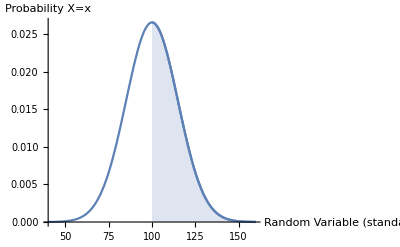

0.5

```mathematica
probabilityNormalDistributionGreaterThan[100,15,100]
```

probabilityNormalDistributionLessThan
Calculates and shows the probability than a random variable is less than the max of a normal distribution with a given mean and standard deviation. numberOfStdevToShow is the same as in the plotting versions. The given plot is just for illustrations. Using this function in manipulate will not change the plot

```mathematica
probabilityNormalDistributionLessThan[mean,standardDeviation,max]
probabilityNormalDistributionLessThan[mean,standardDeviation,max,numberOfStdevToShow]
```

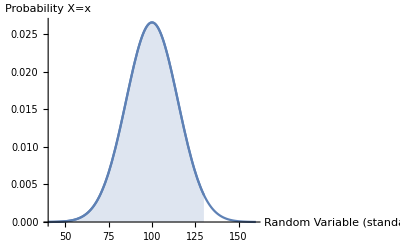

0.97725

```mathematica
probabilityNormalDistributionLessThan[100,15,130]
```

#### Binomial Distribution

probabilityBinomialDistributionBetweenInclusive
Calculates the probability that a random variable that is binomially distributed with n trails and p chance of success is between a and b including a and b. Using this function in manipulate will not change the plot

```mathematica
probabilityBinomialDistributionBetweenInclusive[n,p,a,b]
```

```mathematica
probabilityBinomialDistributionBetweenInclusive[5,0.3,0,3]
```

-Graphics-

0.96922

probabilityBinomialDistributionBetweenExclusive
Calculates the probability that a random variable that is binomially distributed with n trails and p chance of success is between a and b NOT including a and b. Using this function in manipulate will not change the plot

```mathematica
probabilityBinomialDistributionBetweenExclusive[n,p,a,b]
```

```mathematica
probabilityBinomialDistributionBetweenExclusive[5,0.3,0,3]
```

-Graphics-

0.66885

probabilityBinomialDistributionEquals
Calculates the probability that a random variable that is binomially distributed with n trails and p chance of success is equal to a. Using this function in manipulate will not change the plot

```mathematica
probabilityBinomialDistributionEquals[n,p,a]
```

```mathematica
probabilityBinomialDistributionEquals[5,0.3,1]
```

-Graphics-

0.36015

probabilityBinomialDistributionGreaterThan
Calculates the probability that a random variable that is binomially distributed with n trails and p chance of success is greater than but not equal to a. Using this function in manipulate will not change the plot

```mathematica
probabilityBinomialDistributionGreaterThan[n,p,a]
```

```mathematica
probabilityBinomialDistributionGreaterThan[5,0.3,1]
```

-Graphics-

0.47178

probabilityBinomialDistributionLessThan
Calculates the probability that a random variable that is binomially distributed with n trails and p chance of success is less than but not equal to a. Using this function in manipulate will not change the plot

```mathematica
probabilityBinomialDistributionLessThan[n,p,a]
```

```mathematica
probabilityBinomialDistributionLessThan[5,0.3,1]
```

-Graphics-

0.16807

#### Converting Positions on Normal Distributions

Takes a point on one normal distribution and calculates the equivalent on another such that the probabilities won’t change.

```mathematica
convertNormalDistributionValues[meanOfDistribution1,standardDeviationOfDistribution1,valueOnDistribution1,meanOfDistribution2,standardDeviationOfDistribution2]
```

```mathematica
convertNormalDistributionValues[100,15,130,0,1]
```

2

### Statistics

expectedBinomial
Calculates the expected value of a binomial distribution of n trials with p chance of success

```mathematica
expectedBinomial[n,p]
```

```mathematica
expectedBinomial[10,0.5]
```

5.

varianceBinomial
Calculates the variance value of a binomial distribution of n trials with p chance of success

```mathematica
varianceBinomial[n,p]
```

```mathematica
varianceBinomial[10,0.5]
```

2.5

standardDeviationFromVariance
Calculates the standard deviation of a normal distribution from it’s variance

```mathematica
standardDeviationFromVariance[variance]
```

```mathematica
standardDeviationFromVariance[225]
```

15

varianceFromStandardDeviation
Calculates the variance of a normal distribution from it’s standard deviation

```mathematica
varianceFromStandardDeviation[standardDeviation]
```

```mathematica
varianceFromStandardDeviation[15]
```

225

## Complex Numbers (specialist)

ce
Short for ComplexExpand

```mathematica
ce[expression]
```

Cis
Takes an angle and outputs in the form cos(theta)+ⅈsin(theta).

```mathematica
Cis[theta]
```

```mathematica
Cis[π/4]
```

(1+ⅈ)/(√2)

normalise
Full name for Norm

```mathematica
normalise[z]
```

cartesianToPolar
Convert cartesian form to polar form

```mathematica
cartesianToPolar[z]
```

```mathematica
cartesianToPolar[1+√3 ⅈ]
```

2 Cis[π/3]

polarToCartesian
Converts polar form to cartesian form. Can be the result of cartesianToPolar or manually entering the Cis function

```mathematica
polarToCartesian[z]
```

```mathematica
polarToCartesian[2 Cis[π/3]]
```

1+ⅈ √3

```mathematica
polarToCartesian[2*Cis[π/3]]
```

1+ⅈ √3

isConjugateRootTheorumValid
Tests if the conjugate root theorem is valid. Will expand the equation if possible before testing.

```mathematica
isConjugateRootTheorumValid[equasion]
```

```mathematica
isConjugateRootTheorumValid[z^2-z+1]
```

True

```mathematica
isConjugateRootTheorumValid[z^3+(1-ⅈ)z^2-1]
```

False

```mathematica
isConjugateRootTheorumValid[(z+ⅈ)(z-ⅈ)]
```

True

## Kinematics, Mechanics, Statics, Dynamics

resolveForces
Resolves a force of a given magnitude at an angle from the x axis

```mathematica
resolveForces[magnitude,angle]
```

```mathematica
resolveForces[10g,π/6]
```

{5 g,5 √3 g}

### Kinematics

accellerationFromVelocityT
Calculates acceleration(time) from velocity(time)

```mathematica
accellerationFromVelocityT[velocity,time]
```

accellerationFromVelocityT[velocity,time]

```mathematica
accellerationFromVelocityT[2 t^2,t]
```

accellerationFromVelocityT[2 t^2,t]

accellerationFromPositionT
Calculates acceleration(time) from position(time)

```mathematica
accellerationFromPositionT[position,time]
```

accellerationFromPositionT[position,time]

```mathematica
accellerationFromPositionT[Sin[t]+t,t]
```

accellerationFromPositionT[t+Sin[t],t]

velocityFromPositionT
Calculates velocity(time) from position(time)

```mathematica
velocityFromPositionT[position,time]
```

velocityFromPositionT[position,time]

```mathematica
velocityFromPositionT[e^(2t),t]
```

velocityFromPositionT[e^(2 t),t]

accelerationFromVolocityX
Calculates acceleration(time) from velocity(position)

```mathematica
accelerationFromVolocityX[velocity,position]
```

accelerationFromVolocityX[velocity,position]

```mathematica
accelerationFromVolocityX[2v,v]
```

accelerationFromVolocityX[2 v,v]

## Functions and Polynomials

### Polynomials

quadraticFormula
Applies the quadratic formula to the coefficients of a polynomial and simplifies where posible

```mathematica
quadraticFormula[variable,a,b,c]
```

```mathematica
quadraticFormula[x,1,2,-3]
```

{{x→1},{x→-3}}

completeTheSquareCoefficiants
completes the square for the coefficients of a quadratic

```mathematica
completeTheSquareCoefficiants[variable,a,b,c]
```

```mathematica
completeTheSquareCoefficiants[x,1,2,-3]
```

-4+(1+x)^2

completeTheSquarePolynomial
Completes the square for a quadratic function

```mathematica
completeTheSquarePolynomial[function,variable]
```

```mathematica
completeTheSquarePolynomial[x^2+2x-3,x]
```

-4+(1+x)^2

### Even and Odd Functions

evenFunction
Tests if a function is even. If the result is true then the function is definitely even. If the result is not true they it is most likely not even, however there are some exceptions. Trigonometric functions must be entered as Sin[x] NOT Sin.

```mathematica
evenFunction[equasions,variable]
```

```mathematica
evenFunction[Cos[x],x]
```

evenFunction[Cos[x],x]

```mathematica
evenFunction[x^3,x]
```

evenFunction[x^3,x]

oddFunction
Tests if a function is odd. If the result is true then the function is definitely odd. If the result is not true they it is most likely not odd, however there are some exceptions. Trigonometric functions must be entered as Sin[x] NOT Sin.

```mathematica
oddFunction[x^3,x]
```

True

```mathematica
oddFunction[Cos[x],x]
```

Cos[x]==0

### Functional Equations

identifyFunctionalEquasions
Takes an equations and tries to match it to one of the 4 classes of functional equations in the SUP

```mathematica
identifyFunctionalEquasions[equasion,variable]
```

```mathematica
identifyFunctionalEquasions[Log[x],x]
```

f(xy)=f(x)+f(y), f(x)=aLog_b(x) where x>0

```mathematica
identifyFunctionalEquasions[x*Log[x],x]
```

Could not find a function equasion. This does not mean one does not exist

findEquasionToSatisfyFunctionalEquasion
Takes a functional equation and identifies which of the 4 from the sup it is and what f(x) fits is. If the the equation is in only one variable, than the variable 2 parameter can be left as anything. If the equation is in only one variable and has a f(2x) in it then variable2 must equal variable1.

```mathematica
findEquasionToSatisfyFunctionalEquasion[equasion,function,variable1,variable2]
```

```mathematica
findEquasionToSatisfyFunctionalEquasion[f[x+y]==f[y]*f[x],f,x,y]
```

f(x+y)=f(x)f(y), f(x)=a^x

```mathematica
findEquasionToSatisfyFunctionalEquasion[f[x]==-f[x],f,x,y]
```

Could not find a function equasion. This does not mean one does not exist

```mathematica
findEquasionToSatisfyFunctionalEquasion[f[x+x]==f[x]^2,f,x,x]
```

f(x+y)=f(x)f(y), f(x)=a^x

```mathematica
findEquasionToSatisfyFunctionalEquasion[f[x+y]==x*f[y]*y*f[x],f,x,y]
```

Could not find a function equasion. This does not mean one does not exist

trailAndErrorFindEquasionToSatisfyFunctionalEquasion
For use on multiple choice when a function equation is given and you have to identify which function corresponds to it.

```mathematica
trailAndErrorFindEquasionToSatisfyFunctionalEquasion[equasions,function,variable1,variable2,posibleSolutions]
```

```mathematica
trailAndErrorFindEquasionToSatisfyFunctionalEquasion[f[x*y]==x*f[y]+y*f[x],f,x,y,{-x^2,3^x,2x,-3x*Log[x],2*Log[x]},x]
```

-3 x Log[x]

```mathematica
trailAndErrorFindEquasionToSatisfyFunctionalEquasion[f[x*y]==x*f[y]+y*f[x],f,x,y,{-x^2,3^x,2x,2*Log[x]},x]
```

Could not find a function equasion. This does not mean one does not exist

### Matrix Transformations

matrix2x2
Easy way to enter a two by two matrix

```mathematica
matrix2x2[a,b,c,d]//MatrixForm
```

(a | b
c | d)

matrix1x2
Easy way to enter a one by two matrix

```mathematica
matrix1x2[a,b]//MatrixForm
```

(a
b)

transformFunctionByMatrix
Transforms a function by a matrix. This works for matrix to give inverse functions as well as normal matrices (see second example). If no translation is required it can be omitted, however a dilation matrix must be provided even it is is (1 | 0
0 | 1), the identity matrix (which means it does not dilate the function in any way).
note: the workings are meant to be an indicator of what is going on and what to write. You should not blindly copy them with out sanity checking it makes sense first.

```mathematica
transformFunctionByMatrix[function,x,y,dilationMatric,TranslationMatrix]
```

```mathematica
transformFunctionByMatrix[x^2,x,y,matrix2x2[a,0,0,b],matrix1x2[c,d]]
```

Workings:

(a | 0
0 | b).(x
y)+(c
d)=(x'
y')

(c+a x
d+b y)=(x'
y')

{c+a x==x'
d+b y==y'}

{(-c+x')/a==x
d+b x^2==y'}

y'==d+b ((-c+x')/a)^2

Answer:

d+(b (-c+x')^2)/a^2

```mathematica
transformFunctionByMatrix[x^2,x,y,matrix2x2[0,1,1,0]]
```

Workings:

(0 | 1
1 | 0).(x
y)+(0
0)=(x'
y')

(y
x)=(x'
y')

{y==x'
x==y'}

{±(-√x')==x
x==y'}

y'==±(-√x')

Answer (depending on domain of f):

{-√x',√x'}

### Range of Function

rangeOfFunction
Calculates the range of a function. The domain may be omitted if you want it to be x∈(-∞,∞). The domain must be specified as an inequality of any valid form.

```mathematica
rangeOfFunction[function,variable,domainInequality]
```

```mathematica
rangeOfFunction[x^2,x,1<x≤4]
```

(1,16]

1<x≤16

```mathematica
rangeOfFunction[x^2,x,-2<x]
```

[0,∞)

x≥0

### Period of Functions

FunctionPeriod
Calculates the period of a function.
note: this is not my code, it is part of Mathematica

```mathematica
FunctionPeriod[function,variable]
```

```mathematica
FunctionPeriod[2*Tan[(3*π*x)/4],x]
```

4/3

## Other

### Mathematica causing errors

clearEverything
Clears EVERYTHING the user defined. ClearAll does not do this. ClearAll only clears what you put in it. This will clear variables, functions, things you accidentally defined that are causing errors.

```mathematica
clearEverything[]
```

resetMathematica
Quits the kernel and starts a new one. Should do the same as aborting evaluation and then using clearEverything however Mathematica is weird and this is more likely to stop errors.

```mathematica
resetMathematica[]
```

### Need inspiration?

inspirationalQuotesForTheExam
Will return an inspirational quote from a JMSS teacher when and only when you are in the exam.

```mathematica
inspirationalQuotesForTheExam[]
```

## Raw Code

You must shift enter ALL of this code for it to work

```mathematica
convertNormalDistributionValues[mean1_,stdev1_,val_,mean2_,stdev2_]:=mean2+(stdev2*((val-mean1)/stdev1))
enclosedArea[f1_,f2_,x_]:=Module[{i,var,intersections,min,max},
var=x[[1]];
intersections=DeleteDuplicates[roots[f2-f1,var]];
min=intersections[[1,1]];
max=intersections[[1,1]];
For[i=1,i≤Length[intersections],i++,
If[intersections[[i,1]]<min,min=intersections[[i,1]]];
If[intersections[[i,1]]>max,max=intersections[[i,1]]];
];
If[x[[2]]>min,min=x[[2]]];
If[x[[3]]<max,max=x[[3]]];
Return[boundedArea[f2-f1,{var,min,max}]];
];
rangeOfFunction[f_,x_,sdom_:True]:=Module[{i,skippedIfStatment,keyPoints,endPoints,yEndPoints,vAsy,min,max,op1,op2,bracket1,bracket2},
keyPoints=turningPoints[f,x,sdom][[All,1]];
skippedIfStatment=True;
endPoints={};
If[sdom,skippedIfStatment=False];
If[skippedIfStatment,
If[Length[sdom]==2,
AppendTo[endPoints,valueOfInequality[sdom,x]];
,
AppendTo[endPoints,sdom[[1]]];
AppendTo[endPoints,sdom[[3]]];
If[sdom[[0]]==Inequality,
endPoints={};
AppendTo[endPoints,sdom[[1]]];
AppendTo[endPoints,sdom[[5]]];
];
];
];
yEndPoints=f/.x->endPoints;
keyPoints=f/.x->keyPoints;
If[skippedIfStatment,
If[Or[
And[Length[sdom]==2,sdom[[1]]==x,Or[sdom[[0]]==Less,sdom[[0]]==LessEqual]],
And[Length[sdom]==2,sdom[[2]]==x,Or[sdom[[0]]==Greater,sdom[[0]]==GreaterEqual]],
],
AppendTo[keyPoints,Limit[f,x->-∞]];
];
If[Or[
And[Length[sdom]==2,sdom[[1]]==x,Or[sdom[[0]]==Greater,sdom[[0]]==GreaterEqual]],
And[Length[sdom]==2,sdom[[2]]==x,Or[sdom[[0]]==Less,sdom[[0]]==LessEqual]],
],
AppendTo[keyPoints,Limit[f,x->∞]];
];
,
AppendTo[keyPoints,Limit[f,x->-∞]];
AppendTo[keyPoints,Limit[f,x->∞]];
];
vAsy=verticleAsymptotes[f,x];
For[i=1,i≤Length[vAsy],i++,
If[Not[FullSimplify[x==vAsy[[i]]&&sdom]],
Continue[];
];
AppendTo[keyPoints,Limit[f,x->vAsy[[i]],Direction->"FromAbove"]];
AppendTo[keyPoints,Limit[f,x->vAsy[[i]],Direction->"FromBelow"]];
];
keyPoints=DeleteDuplicates[keyPoints];
min=Min[Join[keyPoints,yEndPoints]];
max=Max[Join[keyPoints,yEndPoints]];
op1:=LessEqual;
op2:=LessEqual;
If[min==-∞,op1:=Less];
If[max==∞,op2:=Less];

If[And[Length[sdom]==5,sdom[[0]]==Inequality,min==f/.x->sdom[[1]]],
op1:=sdom[[2]];
];
If[And[Length[sdom]==5,sdom[[0]]==Inequality,min==f/.x->sdom[[5]]],
op1:=sdom[[4]];
];
If[And[Length[sdom]==5,sdom[[0]]==Inequality,max==f/.x->sdom[[1]]],
op2:=sdom[[2]];
];
If[And[Length[sdom]==5,sdom[[0]]==Inequality,max==f/.x->sdom[[5]]],
op2:=sdom[[4]];
];
If[And[Length[sdom]==3,min==f/.x->sdom[[1]]],
op1:=sdom[[0]];
];
If[And[Length[sdom]==3,min==f/.x->sdom[[3]]],
op1:=sdom[[0]];
];
If[And[Length[sdom]==3,max==f/.x->sdom[[1]]],
op2:=sdom[[0]];
];
If[And[Length[sdom]==3,max==f/.x->sdom[[3]]],
op2:=sdom[[0]];
];
If[And[Length[sdom]==2,sdom[[1]]==x,min==f/.x->sdom[[2]]],
If[sdom[[0]]==Less,op1:=Less];
If[sdom[[0]]==Greater,op1:=Less];
];
If[And[Length[sdom]==2,sdom[[2]]==x,min==f/.x->sdom[[1]]],
If[sdom[[0]]==Less,op1:=Less];
If[sdom[[0]]==Greater,op1:=Less];
];
If[And[Length[sdom]==2,sdom[[1]]==x,max==f/.x->sdom[[2]]],
If[sdom[[0]]==Less,op2:=Less];
If[sdom[[0]]==Greater,op2:=Less];
];
If[And[Length[sdom]==2,sdom[[2]]==x,max==f/.x->sdom[[1]]],
If[sdom[[0]]==Less,op2:=Less];
If[sdom[[0]]==Greater,op2:=Less];
];

bracket1="[";
If[op1==Less,
bracket1="(";
];
bracket2="]";
If[op2==Less,
bracket2=")";
];
Print[bracket1,min,",",max,bracket2];
Return[FullSimplify[op1[min,x]&&op2[x,max]]];
];
matrix2x2[a_,b_,c_,d_]:={{a,b},{c,d}}
matrix1x2[a_,b_]:={{a},{b}}
transformFunctionByMatrix[f_,x_,y_,Smat_,Tmat_:{{0},{0}}]:=Module[{xdash,plusminus},
Print["Workings:"];
Print[Smat//MatrixForm,".",{{x},{y}}//MatrixForm,"+",Tmat//MatrixForm,"=",{{x'},{y'}}//MatrixForm];
Print[(Smat.{{x},{y}}+Tmat)//MatrixForm,"=",{{x'},{y'}}//MatrixForm];
Print[{Column[{(Smat.{{x},{y}}+Tmat)[[1,1]]==x',(Smat.{{x},{y}}+Tmat)[[2,1]]==y'}]}];
plusminus=False;
If[Length[Solve[(Smat.{{x},{f}}+Tmat)[[1,1]]==xdash,x]]==2,plusminus=True];
If[plusminus,
Print[{Column[{(±Solve[(Smat.{{x},{f}}+Tmat)[[1,1]]==xdash,x][[1,1,2]]==x)/.xdash->x',(Smat.{{x},{f}}+Tmat)[[2,1]]==y'}]}];
Print[y'==((Smat.{{x},{f}}+Tmat)[[2,1]]/.x->HoldForm[Evaluate[±Solve[(Smat.{{x},{f}}+Tmat)[[1,1]]==xdash,x][[1,1,2]]/.xdash->x']])];
Print["Answer (depending on domain of f):"];
Return[{((Smat.{{x},{f}}+Tmat)[[2,1]]/.x->(Solve[xdash==(Smat.{{x},{f}}+Tmat)[[1,1]],x][[1,1,2]]))/.xdash->x',((Smat.{{x},{f}}+Tmat)[[2,1]]/.x->(-Solve[xdash==(Smat.{{x},{f}}+Tmat)[[1,1]],x][[1,1,2]]))/.xdash->x'}];
,
Print[{Column[{(Solve[(Smat.{{x},{f}}+Tmat)[[1,1]]==xdash,x][[1,1,2]]==x)/.xdash->x',(Smat.{{x},{f}}+Tmat)[[2,1]]==y'}]}];
Print[y'==((Smat.{{x},{f}}+Tmat)[[2,1]]/.x->HoldForm[Evaluate[Solve[(Smat.{{x},{f}}+Tmat)[[1,1]]==xdash,x][[1,1,2]]/.xdash->x']])];
Print["Answer:"];
Return[((Smat.{{x},{f}}+Tmat)[[2,1]]/.x->(Solve[xdash==(Smat.{{x},{f}}+Tmat)[[1,1]],x][[1,1,2]]))/.xdash->x'];
];
];
averageRateOfChange[f_,x_,a_,b_]:=1/(b-a)*((f/.x->b)-(f/.x->a))
nAverageRateOfChange[f_,x_,a_,b_]:=N[1/(b-a)*((f/.x->b)-(f/.x->a))]
resolveForces[magnitude_,angle_]:={Sin[angle]*magnitude,Cos[angle]*magnitude}
accellerationFromVelocityT[v_,t_]:=D[v,t]
accellerationFromPositionT[x_,t_]:=D[x,{t,2}]
velocityFromPositionT[x_,t_]:=D[x,t]
accelerationFromVolocityX[v_,x_]:=v*D[v,x]
solidOfRevolutionAroundX[y_,x_,a_,b_]:=π*Integrate[y^2,{x,a,b}]
solidOfRevolutionAroundY[x_,y_,a_,b_]:=π*Integrate[x^2,{y,a,b}]
nSolidOfRevolutionAroundX[y_,x_,a_,b_]:=π*NIntegrate[y^2,{x,a,b}]
nSolidOfRevolutionAroundY[x_,y_,a_,b_]:=π*NIntegrate[x^2,{y,a,b}]
D2[f_,x_]:=D[f,{x,2}]
solveForDyDx[eq_,x_,y_]:=Solve[eq,y'[x]]
implicityD[f_,x_,y_,pow_:1]:=D[f/.y->y[x],{x,pow}]
nonSignedIntegral[f_,x_]:=Abs[Integrate[f,x]]
semiEvaluateIntegral[f_,x_,a_,b_,c_:0]:=Abs[Integrate[f,{x,a,b}]]==c//HoldForm
boundedArea[f_,x_]:=
Module[{var,roots,total},
var=x[[1]];
roots=Reduce[f<0&&x[[2]]≤var≤x[[3]],var];
total=0;
If[roots[[0]]==Or,
If[x[[2]]≠roots[[1,1]],
total=total+nonSignedIntegral[f,{var,x[[2]],roots[[1,1]]}];
Print[semiEvaluateIntegral[f,var,x[[2]],roots[[1,1]],nonSignedIntegral[f,{var,x[[2]],roots[[1,1]]}]]];
];
For[i=1,i≤Length[roots],i++,
If[i>1,
total=total+nonSignedIntegral[f,{var,roots[[i-1,5]],roots[[i,1]]}];
Print[semiEvaluateIntegral[f,var,roots[[i-1,5]],roots[[i,1]],nonSignedIntegral[f,{var,roots[[i-1,5]],roots[[i,1]]}]]];
];
total=total+nonSignedIntegral[f,{var,roots[[i,1]],roots[[i,5]]}];
Print[semiEvaluateIntegral[f,var,roots[[i,1]],roots[[i,5]],nonSignedIntegral[f,{var,roots[[i,1]],roots[[i,5]]}]]];
];
If[roots[[i-1,5]]≠x[[3]],
total=total+nonSignedIntegral[f,{var,roots[[i-1,5]],x[[3]]}];
Print[semiEvaluateIntegral[f,var,roots[[i-1,5]],x[[3]],nonSignedIntegral[f,{var,roots[[i-1,5]],x[[3]]}]]];
];
];
If[roots[[0]]==Inequality,
If[x[[2]]≠roots[[1]],
total=total+nonSignedIntegral[f,{var,x[[2]],roots[[1]]}];
Print[semiEvaluateIntegral[f,var,x[[2]],roots[[1]],nonSignedIntegral[f,{var,x[[2]],roots[[1]]}]]];
];
total=total+nonSignedIntegral[f,{var,roots[[1]],roots[[5]]}];
Print[semiEvaluateIntegral[f,var,roots[[1]],roots[[5]],nonSignedIntegral[f,{var,roots[[1]],roots[[5]]}]]];
If[roots[[5]]≠x[[3]],
total=total+nonSignedIntegral[f,{var,roots[[5]],x[[3]]}];
Print[semiEvaluateIntegral[f,var,roots[[5]],x[[3]],nonSignedIntegral[f,{var,roots[[5]],x[[3]]}]]];
];
];
Return[total];
]
approximateIntegral[f_,x_,direction_,interval_]:=Module[{var,pos,total},
var=x[[1]];
total=0;
If[And[direction≠"left",direction≠"right"],Return["direction must either be \"left\" or \"right\""]];
If[direction=="left",
For[pos=x[[2]],pos<x[[3]],pos+=interval,
total+=(f/.var->pos)*interval
];
];
If[direction=="right",
For[pos=x[[2]]+interval,pos≤x[[3]],pos+=interval,
total+=(f/.var->pos)*interval
];
];
Return[total];
];
approximateIntegralPlot[f_,x_,direction_,interval_]:=Module[{var,pos,rectangles},
var=x[[1]];
rectangles={};
If[And[direction≠"left",direction≠"right"],Return["direction must either be \"left\" or \"right\""]];
If[direction=="left",
For[pos=x[[2]],pos<x[[3]],pos+=interval,
AppendTo[rectangles,Rectangle[{pos,0},{pos+interval,(f/.var->pos)}]];
];
];
If[direction=="right",
For[pos=x[[2]],pos<x[[3]],pos+=interval,
AppendTo[rectangles,Rectangle[{pos,0},{pos+interval,(f/.var->pos+interval)}]];
];
];
Return[Plot[f,x,Epilog->{FaceForm[Red],EdgeForm[None],Opacity[0.3],rectangles}]];
];
averageValueOfFunction[f_,x_,a_,b_]:=1/(b-a)*Integrate[f,{x,a,b}]
nAverageValueOfFunction[f_,x_,a_,b_]:=1/(b-a)*NIntegrate[f,{x,a,b}]
plotBinomialDistributionBetweenInclusive[n_,p_,a_Integer,b_Integer]:=Module[{i,plot1,plots},
plot1=DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,0,n},ExtentSize->Right,Filling->Axis,FillingStyle->Red];
plots={};
For[i=a,i≤b,i++,
AppendTo[plots,DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,i,i},ExtentSize->Right,Filling->Axis,FillingStyle->Blue]];
];
Return[Show[plot1,plots]];
];
plotBinomialDistributionBetweenExclusive[n_,p_,a_Integer,b_Integer]:=Module[{i,plot1,plots},
plot1=DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,0,n},ExtentSize->Right,Filling->Axis,FillingStyle->Red];
plots={};
For[i=a+1,i≤b-1,i++,
AppendTo[plots,DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,i,i},ExtentSize->Right,Filling->Axis,FillingStyle->Blue]];
];
Return[Show[plot1,plots]];
];
plotBinomialDistributionGreaterThan[n_,p_,a_Integer]:=Module[{i,plot1,plots},
plot1=DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,0,n},ExtentSize->Right,Filling->Axis,FillingStyle->Red];
plots={};
For[i=a+1,i≤n,i++,
AppendTo[plots,DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,i,i},ExtentSize->Right,Filling->Axis,FillingStyle->Blue]];
];
Return[Show[plot1,plots]];
];
plotBinomialDistributionLessThan[n_,p_,a_Integer]:=Module[{i,plot1,plots},
plot1=DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,0,n},ExtentSize->Right,Filling->Axis,FillingStyle->Red];
plots={};
For[i=0,i≤a-1,i++,
AppendTo[plots,DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,i,i},ExtentSize->Right,Filling->Axis,FillingStyle->Blue]];
];
Return[Show[plot1,plots]];
];
plotBinomialDistributionEquals[n_,p_,a_Integer]:=Module[{i,plot1,plots},
plot1=DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,0,n},ExtentSize->Right,Filling->Axis,FillingStyle->Red];
plots=DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,a,a},ExtentSize->Right,Filling->Axis,FillingStyle->Blue];
Return[Show[plot1,plots]];
];
probabilityBinomialDistributionBetweenInclusive[n_,p_,a_Integer,b_Integer]:=Module[{i,plot1,plots},
plot1=DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,0,n},ExtentSize->Right,Filling->Axis,FillingStyle->Red];
plots={};
For[i=a,i≤b,i++,
AppendTo[plots,DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,i,i},ExtentSize->Right,Filling->Axis,FillingStyle->Blue]];
];
Print[Show[plot1,plots]];
Return[Probability[a≤x≤b,x\[Distributed]BinomialDistribution[5,0.3]]];
];
probabilityBinomialDistributionBetweenExclusive[n_,p_,a_Integer,b_Integer]:=Module[{i,plot1,plots},
plot1=DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,0,n},ExtentSize->Right,Filling->Axis,FillingStyle->Red];
plots={};
For[i=a+1,i≤b-1,i++,
AppendTo[plots,DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,i,i},ExtentSize->Right,Filling->Axis,FillingStyle->Blue]];
];
Print[Show[plot1,plots]];
Return[Probability[a<x<b,x\[Distributed]BinomialDistribution[5,0.3]]];
];
probabilityBinomialDistributionGreaterThan[n_,p_,a_Integer]:=Module[{i,plot1,plots},
plot1=DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,0,n},ExtentSize->Right,Filling->Axis,FillingStyle->Red];
plots={};
For[i=a+1,i≤n,i++,
AppendTo[plots,DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,i,i},ExtentSize->Right,Filling->Axis,FillingStyle->Blue]];
];
Print[Show[plot1,plots]];
Return[Probability[x>a,x\[Distributed]BinomialDistribution[5,0.3]]];
];
probabilityBinomialDistributionLessThan[n_,p_,a_Integer]:=Module[{i,plot1,plots},
plot1=DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,0,n},ExtentSize->Right,Filling->Axis,FillingStyle->Red];
plots={};
For[i=0,i≤a-1,i++,
AppendTo[plots,DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,i,i},ExtentSize->Right,Filling->Axis,FillingStyle->Blue]];
];
Print[Show[plot1,plots]];
Return[Probability[x<a,x\[Distributed]BinomialDistribution[5,0.3]]];
];
probabilityBinomialDistributionEquals[n_,p_,a_Integer]:=Module[{i,plot1,plots},
plot1=DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,0,n},ExtentSize->Right,Filling->Axis,FillingStyle->Red];
plots=DiscretePlot[PDF[BinomialDistribution[n,p],x],{x,a,a},ExtentSize->Right,Filling->Axis,FillingStyle->Blue];
Print[Show[plot1,plots]];
Return[Probability[x==a,x\[Distributed]BinomialDistribution[5,0.3]]];
];
nPr[n_,r_]:=Factorial[n]/Factorial[n-r]
nCr[n_,r_]:=Factorial[n]/(Factorial[n-r]*Factorial[r])
expectedBinomial[n_,p_]:=n*p
varianceBinomial[n_,p_]:=n*p*(1-p)
standardDeviationFromVariance[variance_]:=√variance
varianceFromStandardDeviation[stdev_]:=stdev^2
probabilityNormalDistributionBetween[mean_,stdev_,a_,b_,numberOfStdevToShow_:4]:=Module[{plot1,plot2},
plot1=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,mean+stdev*numberOfStdevToShow},AxesLabel->{"Random Variable (standard deviation)", "Probability X=x"}];
plot2=Plot[PDF[NormalDistribution[mean,stdev],x],{x,a,b},Filling->Axis,PlotRange->PlotRange[plot1]];
Print[Show[plot1,plot2]];
Return[NProbability[a<x<b,x\[Distributed]NormalDistribution[mean,stdev]]];
];
probabilityNormalDistributionGreaterThan[mean_,stdev_,a_,numberOfStdevToShow_:4]:=Module[{plot1,plot2},
plot1=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,mean+stdev*numberOfStdevToShow},AxesLabel->{"Random Variable (standard deviation)", "Probability X=x"}];
plot2=Plot[PDF[NormalDistribution[mean,stdev],x],{x,a,mean+stdev*numberOfStdevToShow},Filling->Axis,PlotRange->PlotRange[plot1]];
Print[Show[plot1,plot2]];
Return[NProbability[a<x,x\[Distributed]NormalDistribution[mean,stdev]]];
];
probabilityNormalDistributionLessThan[mean_,stdev_,a_,numberOfStdevToShow_:4]:=Module[{plot1,plot2},
plot1=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,mean+stdev*numberOfStdevToShow},AxesLabel->{"Random Variable (standard deviation)", "Probability X=x"}];
plot2=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,a},Filling->Axis,PlotRange->PlotRange[plot1]];
Print[Show[plot1,plot2]];
Return[NProbability[x<a,x\[Distributed]NormalDistribution[mean,stdev]]];
];
evaluateExpression[exp_]:=Evaluate[exp]
doNotevaluateExpression[exp_]:=Unevaluated[exp]
ce[exp_]:=ComplexExpand[exp]
Cis[theta_]:=Cos[theta]+ⅈ*Sin[theta]
CisHold[theta_]:=HoldForm[Cis[theta]]
normalise[z_]:=Norm[z]
cartesianToPolar[z_]:=√(Re[z]^2+Im[z]^2)*CisHold[ArcTan[Im[z]/Re[z]]]
polarToCartesian[z_]:=Expand[ReleaseHold[z]]
isConjugateRootTheorumValid[f_]:=Module[{i,expandedF,result},
expandedF=Expand[f];
If[Im[expandedF]≠0,Return[False]];
If[Im[expandedF]==0,Return[True]];
If[Length[expandedF]≥2,
For[i=1,i≤Length[expandedF],i++,
result=isConjugateRootTheorumValid[expandedF[[i]]];
If[result==False,Return[False]];
];
];
Return[True];
];
identifyFunctionalEquasions[f_,x_]:=Module[{},
If[FullSimplify[(f/.x->(a+b))==(f/.x->(a))+(f/.x->(b))],Return["f(x+y)=f(x)+f(y), f(x)=cx"]];
If[FullSimplify[(f/.x->(a+b))==(f/.x->(a))*(f/.x->(b))],Return["f(x+y)=f(x)f(y), f(x)=a^x"]];
If[FullSimplify[(f/.x->(a*b))==(f/.x->(a))+(f/.x->(b)),a>0&&b>0],Return["f(xy)=f(x)+f(y), f(x)=aLog_b(x) where x>0"]];
If[FullSimplify[(f/.x->(a*b))==(f/.x->(a))*(f/.x->(b))],Return["f(xy)=f(x)f(y), f(x)=x^n"]];
Return["Could not find a function equasion. This does not mean one does not exist"];
];
findEquasionToSatisfyFunctionalEquasion[function_,f_,x_,y_]:=Module[{},
If[FullSimplify[function/.f[x]->a*x/.f[y]->a*y/.f[x+y]->a*(x+y),x>0&&y>0],Return["f(x+y)=f(x)+f(y), f(x)=cx"]];
If[FullSimplify[function/.f[x]->a^x/.f[y]->a^y/.f[x+y]->a^(x+y),x>0&&y>0],Return["f(x+y)=f(x)f(y), f(x)=a^x"]];
If[FullSimplify[function/.f[x]->a*Log[x]/.f[y]->a*Log[y]/.f[x*y]->a*Log[x*y],x>0&&y>0],Return["f(xy)=f(x)+f(y), f(x)=aLog_b(x) where x>0"]];
If[FullSimplify[function/.f[x]->x^n/.f[y]->y^n/.f[x*y]->(x*y)^n,x>0&&y>0],Return["f(xy)=f(x)f(y), f(x)=x^n"]];
Return["Could not find a function equasion. This does not mean one does not exist"];
];
trailAndErrorFindEquasionToSatisfyFunctionalEquasion[function_,f_,x_,y_,options_,ox_]:=Module[{i},
For[i=0,i≤Length[options],i++,
If[FullSimplify[function/.f[x]->(options[[i]]/.ox->x)/.f[y]->(options[[i]]/.ox->y)/.f[x+y]->(options[[i]]/.ox->(x+y))/.f[x*y]->(options[[i]]/.ox->(x*y)),x>0&&y>0],Return[options[[i]]]];
];
Return["Could not find a function equasion. This does not mean one does not exist"];
];
quadraticFormula[var_,a_,b_,c_]:={{var->(-b+√(b^2-4a*c))/(2a)},{var->(-b-√(b^2-4a*c))/(2a)}}
evenFunction[f_,var_]:=FullSimplify[(f/.var->var)==(f/.var->(-var))]
oddFunction[f_,var_]:=FullSimplify[(f/.var->(-var))==(-f/.var->(var))]
completeTheSquareCoefficiants[funcVar_,a_,b_,c_]:=a(funcVar+b/(2a))^2+(c-b^2/(4a))
completeTheSquarePolynomial[f_,funcVar_]:=Coefficient[f,funcVar,2](funcVar+Coefficient[f,funcVar,1]/(2Coefficient[f,funcVar,2]))^2+(Coefficient[f,funcVar,0]-(Coefficient[f,funcVar,1])^2/(4Coefficient[f,funcVar,2]))
clearEverything[]:=Clear["Global`*"]
resetMathematica[]:=Module[{},Quit[];x=0;Clear[x];]
vectorOrigin[i_,j_,k_]:={{0,0,0},{i,j,k}}
vectorFrom[i0_,j0_,k0_,i1_,j1_,k1_]:={{i0,j0,k0},{i1,j1,k1}}
vector[i_,j_,k_]:={i,j,k}
geogebra3DSeption[vec_]:=Module[{i,j,maxRange,d,arrows},
maxRange=0;
d=0;
arrows={};
For[i=1,i≤Length[vec],i++,
AppendTo[arrows,Arrow[vec[[i]]]];
For[j=1,j≤3,j++,
d=Abs[vec[[i,2,j]]-vec[[i,1,j]]];
If[d>maxRange,
maxRange=d;
];
];
];
Return[
Graphics3D[arrows,Axes->{1,1,1},AxesOrigin->{0,0,0},AxesStyle->{Directive[Red,Thick],Directive[Green,Thick],Directive[Blue,Thick]},PlotRange->{{-maxRange,maxRange},{-maxRange,maxRange},{-maxRange,maxRange}}]
];
];
eulersMethod[grad_,y_,x_,increment_,startx_,starty_,endx_,showEvery_:1]:=Module[{i,previousx,previousy,output,count},
output={};
previousx=startx;
previousy=starty;
i=startx;
count=0;
AppendTo[output,{previousx,previousy}];
While[i<endx,
previousx+=increment;
previousy+=increment*(grad/.y[x]->previousy/.x->previousx);
If[Or[Mod[count,showEvery]==0,i+increment≥endx,i==startx],
AppendTo[output,{previousx,previousy}];
];
i+=increment;
count+=1;
];
Return[output];
];
eulersMethodPlot[grad_,dom_,y_,initialCondition_,interval_]:=Module[{gradxy,var,correctSolution,iceq,correctPlot,approximation,approxPlot},
var=dom[[1]];
gradxy=grad/.y->y[var];
iceq=y[initialCondition[[1]]]==initialCondition[[2]];
correctSolution=DSolve[{y'[var]==gradxy,iceq},y[var],var];

approximation=eulersMethod[gradxy,y,var,interval,initialCondition[[1]],initialCondition[[2]],dom[[3]]];
approxPlot=ListLinePlot[approximation,Epilog->{PointSize[Medium],Point[approximation]}];
correctPlot=Plot[correctSolution[[All,1,2]],dom,PlotRange->PlotRange[approxPlot],PlotStyle->Red];
Return[Show[approxPlot,correctPlot]];
];
complexPlot[f_,z_,dom_,ran_]:=ContourPlot[Evaluate[f/.z->(x+ⅈ*y)],{x,dom[[1]],dom[[2]]},{y,ran[[1]],ran[[2]]},Frame->False,Axes->True,AspectRatio->Automatic]
probabilityNormalDistributionBetween[mean_,stdev_,a_,b_,numberOfStdevToShow_:4]:=Module[{plot1,plot2},
plot1=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,mean+stdev*numberOfStdevToShow},AxesLabel->{"Random Variable (standard deviation)", "Probability X=x"}];
plot2=Plot[PDF[NormalDistribution[mean,stdev],x],{x,a,b},Filling->Axis,PlotRange->PlotRange[plot1]];
Print[Show[plot1,plot2]];
Return[NProbability[a<x<b,x\[Distributed]NormalDistribution[mean,stdev]]];
];
probabilityNormalDistributionGreaterThan[mean_,stdev_,a_,numberOfStdevToShow_:4]:=Module[{plot1,plot2},
plot1=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,mean+stdev*numberOfStdevToShow},AxesLabel->{"Random Variable (standard deviation)", "Probability X=x"}];
plot2=Plot[PDF[NormalDistribution[mean,stdev],x],{x,a,mean+stdev*numberOfStdevToShow},Filling->Axis,PlotRange->PlotRange[plot1]];
Print[Show[plot1,plot2]];
Return[NProbability[a<x,x\[Distributed]NormalDistribution[mean,stdev]]];
];
probabilityNormalDistributionLessThan[mean_,stdev_,a_,numberOfStdevToShow_:4]:=Module[{plot1,plot2},
plot1=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,mean+stdev*numberOfStdevToShow},AxesLabel->{"Random Variable (standard deviation)", "Probability X=x"}];
plot2=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,a},Filling->Axis,PlotRange->PlotRange[plot1]];
Print[Show[plot1,plot2]];
Return[NProbability[x<a,x\[Distributed]NormalDistribution[mean,stdev]]];
];
plotNormalDistributionBetween[mean_,stdev_,a_,b_,numberOfStdevToShow_:4]:=Module[{plot1,plot2},
plot1=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,mean+stdev*numberOfStdevToShow},AxesLabel->{"Random Variable (standard deviation)", "Probability X=x"}];
plot2=Plot[PDF[NormalDistribution[mean,stdev],x],{x,a,b},Filling->Axis,PlotRange->PlotRange[plot1]];
Return[Show[plot1,plot2]];
];
plotNormalDistributionGreaterThan[mean_,stdev_,a_,numberOfStdevToShow_:4]:=Module[{plot1,plot2},
plot1=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,mean+stdev*numberOfStdevToShow},AxesLabel->{"Random Variable (standard deviation)", "Probability X=x"}];
plot2=Plot[PDF[NormalDistribution[mean,stdev],x],{x,a,mean+stdev*numberOfStdevToShow},Filling->Axis,PlotRange->PlotRange[plot1]];
Return[Show[plot1,plot2]];
];
plotNormalDistributionLessThan[mean_,stdev_,a_,numberOfStdevToShow_:4]:=Module[{plot1,plot2},
plot1=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,mean+stdev*numberOfStdevToShow},AxesLabel->{"Random Variable (standard deviation)", "Probability X=x"}];
plot2=Plot[PDF[NormalDistribution[mean,stdev],x],{x,mean-stdev*numberOfStdevToShow,a},Filling->Axis,PlotRange->PlotRange[plot1]];
Return[Show[plot1,plot2]];
];
Zip[a_,b_]:=Module[{i, output},
output={};
For[i=1,i≤Length[a],i++,
AppendTo[output,{a[[i]],b[[i]]}];
];
Return[output];
];
roots[f_,x_,sdom_:True]:=Module[{i,rawSol,root,output},
rawSol=Solve[f==0&&sdom,x,Reals];
root={};
output={};
For[i=1,i≤Length[rawSol],i++,
If[rawSol[[i,1,2,0]]==Root,
AppendTo[root,N[rawSol[[i]],2]];
Continue[];
];
AppendTo[root,rawSol[[i]]];
];
If[Or[root=={{}},root=={}],
Return[{}],
For[i=1,i≤Length[root],i++,
AppendTo[output, {root[[i,1,2]],0}];
];
Return[output]
];
];
approximateRoots[solutions_]:=Module[{i, output},
output={};
For[i=1,i≤Length[solutions],i++,
If[solutions[[i,1,2,0]]==Root,
AppendTo[output, N[solutions[[i]],2]];
Continue[];
];
AppendTo[output, solutions[[i]]];
];
Return[output];
];
turningPoints[f_,x_,sdom_:True]:=Module[{solveResult,skippedIfStatment},
skippedIfStatment=True;
If[D[f,x]==0,
skippedIfStatment=False;
solveResult={{}};
];
If[skippedIfStatment,
solveResult=approximateRoots[Solve[D[f,x]==0&&sdom,x,Reals]];
];
If[Or[solveResult=={{}},solveResult=={}],
Return[{}]
,
Return[Zip[solveResult[[All,1,2]],f/.x->solveResult[[All,1,2]]]]
];
Print["The answer is liable to contain errors"];
Return[{}]
];
maximumTurningPoints[f_,x_,sdom_:True]:=Module[{i,TPs,output},
TPs=turningPoints[f,x,sdom];
output={};
If[Or[TPs=={{}},TPs=={},TPs=={}],
Return[{}];
];
For[i=1,i≤Length[TPs],i++,
If[(D[f,{x,2}]/.x->TPs[[i,1]])<0,
AppendTo[output,TPs[[i]]];
];
];
Return[output];
];
minimumTurningPoints[f_,x_,sdom_:True]:=Module[{i,TPs,output},
TPs=turningPoints[f,x,sdom];
output={};
If[Or[TPs=={{}},TPs=={},TPs=={}],
Return[{}];
];
For[i=1,i≤Length[TPs],i++,
If[(D[f,{x,2}]/.x->TPs[[i,1]])>0,
AppendTo[output,TPs[[i]]];
];
];
Return[output];
];
stationaryPointsOfInflection[f_,x_,sdom_:True]:=Module[{i,j,secondDSolutions,thirdDSolutions,output,inflections,shouldAdd,skippedIfStatment},
output={};
inflections={};
shouldAdd=True;
skippedIfStatment=True;
If[D[f,{x,2}]==0,
secondDSolutions={{}};
skippedIfStatment=False;
];
If[skippedIfStatment,
secondDSolutions=approximateRoots[Solve[D[f,{x,2}]==0&&sdom,x,Reals]];
];
skippedIfStatment=True;
If[D[f,{x,3}]==0,
thirdDSolutions={{}};
skippedIfStatment=False;
];
If[skippedIfStatment,
thirdDSolutions=approximateRoots[Solve[D[f,{x,3}]==0&&sdom,x,Reals]];
];
If[Or[secondDSolutions=={{}},secondDSolutions=={}],
Return[{}];
,
If[Or[thirdDSolutions=={{}},thirdDSolutions=={}],
Return[{}];
,
For[i=1,i≤Length[secondDSolutions],i++,
shouldAdd=False;
For[j=1,j≤Length[thirdDSolutions],j++,
If[secondDSolutions[[i]]==thirdDSolutions[[j]],
shouldAdd=True;
];
];
If[shouldAdd,
AppendTo[inflections,secondDSolutions[[i]]];
];
];
Return[Zip[inflections[[All,1,2]],f/.x->inflections[[All,1,2]]]];
];
];
Print["The answer is liable to contain errors"];
Return[{}];
];
movingPointsOfInflection[f_,x_,sdom_:True]:=Module[{i,j,secondDSolutions,thirdDSolutions,output,inflections,shouldAdd,skippedIfStatment},
output={};
inflections={};
shouldAdd=True;
skippedIfStatment=True;
If[D[f,{x,2}]==0,
secondDSolutions={{}};
skippedIfStatment=False;
];
If[skippedIfStatment,
secondDSolutions=approximateRoots[Solve[D[f,{x,2}]==0&&sdom,x,Reals]];
];
skippedIfStatment=True;
If[D[f,{x,3}]==0,
thirdDSolutions={{}};
skippedIfStatment=False;
];
If[skippedIfStatment,
thirdDSolutions=approximateRoots[Solve[D[f,{x,3}]==0&&sdom,x,Reals]];
];
If[Or[secondDSolutions=={{}},secondDSolutions=={}],
Return[{}];
,
If[Or[thirdDSolutions=={{}},thirdDSolutions=={}],
Return[Zip[secondDSolutions[[All,1,2]],f/.x->secondDSolutions[[All,1,2]]]];
,
For[i=1,i≤Length[secondDSolutions],i++,
shouldAdd=True;
For[j=1,j≤Length[thirdDSolutions],j++,
If[secondDSolutions[[i]]==thirdDSolutions[[j]],
shouldAdd=False;
];
];
If[shouldAdd,
AppendTo[inflections,secondDSolutions[[i]]];
];
];
Return[Zip[inflections[[All,1,2]],f/.x->inflections[[All,1,2]]]];
];
];
Print["The answer is liable to contain errors"];
Return[{}];
];
concaviteAtPointAsInteger[f_,x_,p_]:=Module[{secondD},
secondD=D[f,{x,2}];
If[(secondD/.x->p)≤0,
Return[1]
,
Return[-1]
];
Return["Error"];
];
yIntercepts[f_,x_,sdom_:True]:=Module[{},
If[(f&&sdom/.x->0)==False,
Return[{}];
];
Return[{{0,(f&&sdom/.x->0)}}];
];
evalulateValue[val_]:=val
plotColors[n_]:=ColorData[97,"ColorList"][[Mod[n,15]]]
obliqueAsymptote[f_,x_]:=Module[{i,expandedForm,temp,output,hasOAsymptote},
expandedForm=Expand[f];
If[expandedForm[[0]]==Plus,
temp={};
output={};
hasOAsymptote=False;
For[i=1,i≤Length[expandedForm],i++,
If[Limit[expandedForm[[i]],x->∞]≠0,
AppendTo[temp,expandedForm[[i]]];
,
hasOAsymptote=True;
];
];
hasOAsymptote=True;
If[hasOAsymptote,
temp=Total[temp];
AppendTo[output,temp];
If[temp==0,output=Drop[output,-1]];
temp={};
];
hasOAsymptote=False;
For[i=1,i≤Length[expandedForm],i++,
If[Limit[expandedForm[[i]],x->-∞]≠0,
AppendTo[temp,expandedForm[[i]]];
,
hasOAsymptote=True;
];
];
hasOAsymptote=True;
If[hasOAsymptote,
temp=Total[temp];
AppendTo[output,temp];
If[temp==0,output=Drop[output,-1]];
temp={};
];
output=DeleteDuplicates[output];
Return[output];
];
Return[{}];
];
valueOfInequality[inequ_,x_]:=Module[{},
If[inequ[[2]]==x,Return[inequ[[1]]]];
If[inequ[[1]]==x,Return[inequ[[2]]]];
]
verticleAsymptotes[f_,x_]:=Module[{i,j,dom,asymptotes,output},
dom=FunctionDomain[f,x];
asymptotes={};
output={};
For[i=1,i≤Length[dom],i++,
If[dom[[i,0]]==Less,
AppendTo[asymptotes,valueOfInequality[dom[[i]],x]];
];
If[dom[[i,0]]==Greater,
AppendTo[asymptotes,valueOfInequality[dom[[i]],x]];
];
If[dom[[i,0]]==Inequality,
For[j=1,j≤Length[dom[[i]]]-2,j=j+2,
AppendTo[asymptotes,valueOfInequality[dom[[i,j;;j+2]],x]];
];
];
];
asymptotes=DeleteDuplicates[asymptotes];
For[i=1,i≤Length[asymptotes],i++,
If[Or[Limit[f,x->asymptotes[[i]],Direction->"FromAbove"]==∞,Limit[f,x->asymptotes[[i]],Direction->"FromAbove"]==-∞],
AppendTo[output,asymptotes[[i]]];
];
If[Or[Limit[f,x->asymptotes[[i]],Direction->"FromBelow"]==∞,Limit[f,x->asymptotes[[i]],Direction->"FromBelow"]==-∞],
AppendTo[output,asymptotes[[i]]];
];
];
output=DeleteDuplicates[output];
Return[output];
];
horizontalAsymptotes[f_,x_]:=Module[{output,val},
output={};
val=0;
val=Limit[f,x->∞];
If[And[val≠∞,val≠-∞],
AppendTo[output,val];
];
val=Limit[f,x->-∞];
If[And[val≠∞,val≠-∞],
AppendTo[output,val];
];
output=DeleteDuplicates[output];
Return[output];
];
plotinator[f_,dom_,showObliqueAsymptotes_:False]:=Module[{i,j,keyPoints,plot,absoluteRange,epilogPoints,epologTextOffset,epilogs,hAsymptotes,vAsymptotes,oAsymptotes,asymptotes,solveDomain,plotEquasions,oAsymptoteHolder,plotStyle,pointObjects,numberOfEquasions},
keyPoints={};
plot=0;
absoluteRange=0;
epilogPoints=0;
epologTextOffset=0;
epilogs={};
solveDomain=dom[[2]]≤dom[[1]]≤dom[[3]];
plotEquasions={f};
oAsymptoteHolder={};
plotStyle={};
pointObjects={};
numberOfEquasions=0;

If[(f)[[0]]==List,
plotEquasions=f;
];

For[i=1,i≤Length[plotEquasions],i++,
AppendTo[plotStyle,{plotColors[i]}]
];
For[i=1,i≤Length[plotEquasions],i++,
keyPoints=Join[keyPoints,movingPointsOfInflection[plotEquasions[[i]],dom[[1]],solveDomain]];
keyPoints=Join[keyPoints,stationaryPointsOfInflection[plotEquasions[[i]],dom[[1]],solveDomain]];
keyPoints=Join[keyPoints,turningPoints[plotEquasions[[i]],dom[[1]],solveDomain]];
keyPoints=Join[keyPoints,roots[plotEquasions[[i]],dom[[1]],solveDomain]];
keyPoints=Join[keyPoints,yIntercepts[plotEquasions[[i]],dom[[1]],solveDomain]];
];
keyPoints=DeleteDuplicates[keyPoints];

plot=Plot[f,dom];
absoluteRange=Abs[PlotRange[plot][[2,2]]-PlotRange[plot][[2,1]]];
For[j=1,j≤Length[plotEquasions],j++,
For[i=1,i≤Length[keyPoints],i++,
epologTextOffset=1/10*absoluteRange*concaviteAtPointAsInteger[plotEquasions[[j]],dom[[1]],keyPoints[[i,1]]];
AppendTo[epilogs,Text[keyPoints[[i]],{keyPoints[[i,1]],keyPoints[[i,2]]+epologTextOffset}]];
];
];

asymptotes={};
For[j=1,j≤Length[plotEquasions],j++,
hAsymptotes=horizontalAsymptotes[plotEquasions[[j]],dom[[1]]];
vAsymptotes=verticleAsymptotes[plotEquasions[[j]],dom[[1]]];
oAsymptotes=obliqueAsymptote[plotEquasions[[j]],dom[[1]]];
For[i=1,i≤Length[hAsymptotes],i++,
AppendTo[asymptotes,Tooltip[Line[{{dom[[2]],hAsymptotes[[i]]},{dom[[3]],hAsymptotes[[i]]}}],y==hAsymptotes[[i]]]];
];
For[i=1,i≤Length[vAsymptotes],i++,
AppendTo[asymptotes,Tooltip[Line[{{vAsymptotes[[i]],PlotRange[plot][[2,1]]},{vAsymptotes[[i]],PlotRange[plot][[2,2]]}}],x==vAsymptotes[[i]]]];
];
For[i=1,i≤Length[oAsymptotes],i++,
AppendTo[oAsymptoteHolder,oAsymptotes[[i]]];
];
];

If[showObliqueAsymptotes,
Print["showing oblique asymptotes"];
oAsymptoteHolder=DeleteDuplicates[oAsymptoteHolder];
For[i=1,i≤Length[oAsymptoteHolder],i++,
AppendTo[plotEquasions,oAsymptoteHolder[[i]]];
];

For[i=1,i≤(Length[oAsymptoteHolder]),i++,
AppendTo[plotStyle,{Red,Dashed}];
];
];

For[i=1,i≤Length[keyPoints],i++,
AppendTo[pointObjects,Tooltip[Point[keyPoints[[i]]],{keyPoints[[i,1]],keyPoints[[i,2]]}]];
];

plot=Plot[plotEquasions,dom,Epilog->{PointSize[Large],pointObjects,(*epilogs,*)Directive[Red,Dashed],asymptotes},PlotStyle->plotStyle,PlotLegends->"Expressions"];
Return[plot];
];
inspirationalQuotesForTheExam[]:=Module[{encryptedQuotes},
encryptedQuotes={{EncryptedObject[…],EncryptedObject[…],EncryptedObject[…],EncryptedObject[…]},{EncryptedObject[…],EncryptedObject[…],EncryptedObject[…],EncryptedObject[…]},{EncryptedObject[…],EncryptedObject[…],EncryptedObject[…],EncryptedObject[…]},{EncryptedObject[…],EncryptedObject[…],EncryptedObject[…],EncryptedObject[…]},{EncryptedObject[…],EncryptedObject[…],EncryptedObject[…],EncryptedObject[…]},{EncryptedObject[…],EncryptedObject[…],EncryptedObject[…],EncryptedObject[…]},{EncryptedObject[…],EncryptedObject[…],EncryptedObject[…],EncryptedObject[…]},{EncryptedObject[…],EncryptedObject[…],EncryptedObject[…],EncryptedObject[…]},{EncryptedObject[…],EncryptedObject[…],EncryptedObject[…],EncryptedObject[…]},{EncryptedObject[…],EncryptedObject[…],EncryptedObject[…],EncryptedObject[…]},{EncryptedObject[…],EncryptedObject[…],EncryptedObject[…],EncryptedObject[…]},{EncryptedObject[…],EncryptedObject[…],EncryptedObject[…],EncryptedObject[…]},{EncryptedObject[…],EncryptedObject[…],EncryptedObject[…],EncryptedObject[…]}};
Quiet[Check[ToExpression[Decrypt[ToString[Floor[(Now[[1,3]]-1)/4]],EncryptedObject[…]]],Return["You cannot run this function outside the exam"]]];
];
```